```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
ClearAll[A1];
A1=1/u(-((18 m u+9 u^2+4 m^2 (2+3 u^3)) Derivative[0,1][f][m,u])+(27 u^2-64 m^3 u^2-128 m^4 u^4-24 m^2 (-1+6 u^3)+m (52 u-108 u^4)) (2 Derivative[0,1][f][m,u]+u Derivative[0,2][f][m,u])-(8 m+9 u) (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4) (6 Derivative[0,1][f][m,u]+u (6 Derivative[0,2][f][m,u]+u Derivative[0,3][f][m,u])));
```

```mathematica
A2 = Simplify[A1/.{f->Function[{m,u},ff[m^3,u/m]]}/.{m->l^(1/3),u->U l^(1/3)}]
```

-((8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5) ff^(0,1)[l,U])/U+(-24-50 U+(-27+320 l) U^2+2016 l U^3+4 (783-224 l) l U^4-54 l (-27+16 l) U^5) ff^(0,2)[l,U]-U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) ff^(0,3)[l,U]

```mathematica
Coefficient[A2, {Derivative[0,3][ff][l,U],Derivative[0,2][ff][l,U],Derivative[0,1][ff][l,U]}]
```

{-U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4),-24-50 U+(-27+320 l) U^2+2016 l U^3+4 (783-224 l) l U^4-54 l (-27+16 l) U^5,-(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/U}

```mathematica
D4[l_,U_]:=1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4;
Q4[l_,U_]:=1-8l U^2-24U^3+16l^2U^4;
Q6[l_,U_]:=1-12U^2l-36U^3l+48U^4l^2+144U^5l^2+U^6l^2(216-64l);
```

```mathematica
A3=Simplify[A2/.ff->Function[{l,U},Integrate[a[l,U]/U, U]]]
```

2 l (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3) a[l,U]+((-8-16 U+3 (-3+64 l) U^2+1296 l U^3+4 (513-160 l) l U^4+36 (27-16 l) l U^5) a^(0,1)[l,U])/U-(8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) a^(0,2)[l,U]

```mathematica
{a2,a1,a0}=Simplify[Coefficient[A3,{Derivative[0,2][a][l,U],Derivative[0,1][a][l,U],a[l,U]}]]
```

{-((8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),-16-8/U+3 (-3+64 l) U+1296 l U^2+4 (513-160 l) l U^3+36 (27-16 l) l U^4,2 l (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3)}

```mathematica
P[l_,U_]=Together[a1/a2]
```

(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4))

```mathematica
Q[l_,U_]=Together[a0/a2]
```

(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4))

```mathematica
matA[l_,U_]:={{0, 1}, {-Q[l,U], -P[l, U]}};
```

```mathematica
A4=Simplify[A3/a2]
```

(2 l U (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3) a[l,U]+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) a^(0,1)[l,U]+U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) a^(0,2)[l,U])/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

```mathematica
Simplify[A4/.{a->Function[{l,U},U^r(1+b1 U+b2 U^2)]}]
Simplify[Series[%,{U,0,2}]]
```

(U^(-2+r) (2 l U^2 (1+b1 U+b2 U^2) (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3)+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) (U (b1+2 b2 U)+r (1+b1 U+b2 U^2))+(8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) (2 b2 U^2+r^2 (1+b1 U+b2 U^2)+r (-1+b1 U+3 b2 U^2))))/((8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

U^r (r^2/U^2+(-r/8+b1 (1+r)^2)/U+(-8 l+(17 r)/64-16 l r-1/8 b1 (1+r)+b2 (2+r)^2)+O[U]^1)

```mathematica
Simplify[A4/.{a->Function[{l,U},(U+8/9)^r(1+b1 (U+8/9)+b2 (U+8/9)^2)]}]
Simplify[Series[%,{U,-8/9,1}]]
```

((8/9+U)^r (-18 l U (8+9 U) (32+282 U-6 (-81+32 l) U^2-9 (-27+16 l) U^3) (1+b1 (8/9+U)+b2 (8/9+U)^2)+(8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5) (81 r+9 b1 (1+r) (8+9 U)+b2 (2+r) (8+9 U)^2)+9 U (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) (b2 (2+3 r+r^2) (8+9 U)^2+9 r (9 (-1+r)+b1 (1+r) (8+9 U)))))/(9 U (8+9 U)^2 (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

(8/9+U)^r (((-2+r) r)/(U+8/9)^2+(b1 (-1+r^2)+(9 (189 r-256 l (-1+5 r)))/(8 (27+256 l)))/(U+8/9)+1/(64 (27+256 l)^2)(65536 l^2 (324+(-405+128 b2) r+64 b2 r^2)+6912 l (-567+2 (81+128 b2) r+128 b2 r^2)+729 r (-5265+64 b2 (2+r))-72 b1 (27+256 l) (-189 (1+r)+256 l (4+5 r)))-1/(512 (27+256 l)^3)9 (72 b1 (27+256 l) (47385 (1+r)-6912 l (-5+2 r)+65536 l^2 (1+5 r))+64 b2 (27+256 l)^2 (-189 (2+r)+256 l (9+5 r))+81 (-10058013 r+16777216 l^3 (-7+5 r)+5308416 l^2 (3+5 r)-186624 l (80+69 r))) (U+8/9)+O[U+8/9]^2)

```mathematica
l0=1;
```

```mathematica
U0=U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]]
```

{,,,}

```mathematica
Simplify[A4/.{a->Function[{l,U},(U-U0[[4]])^r]}]
Simplify[Series[%,{U,U0[[4]],0}]]
```

((2 l U (-32-282 U+6 (-81+32 l) U^2+9 (-27+16 l) U^3)+((-1+r) r U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))/((U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)+(r (8+16 U+(9-192 l) U^2-1296 l U^3+4 l (-513+160 l) U^4+36 l (-27+16 l) U^5))/(U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)) (U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^r)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

(U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^r (((-1+r) r)/((U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)+(r (8+16 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+9 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+64 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (10+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)-12 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (16+108 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+171 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3)))/(Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044) (1+Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+16 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4-l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+36 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+27 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)) (U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044))+(2 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044) (-32-314 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044-768 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2-729 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3-243 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+768 l^3 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6 (4+3 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)-32 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (64+393 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+567 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+243 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3)+l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (448+3744 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+15048 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+27054 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+21870 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+6561 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^5))-r (64+272 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+416 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+288 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+1024 l^4 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^8 (80+180 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+81 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2)-128 l^3 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6 (256+2880 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+7506 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+7047 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+2187 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4)+4 l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3 (1792+7524 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+12042 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+8505 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+2187 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4)+4 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4 (512+28288 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+156528 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2+364176 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^3+425736 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4+249318 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^5+59049 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^6)))/((Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+9 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (1+Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+16 l^2 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^4-l (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2 (8+36 Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044+27 (Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044)^2))^2)+O[U-Root0.136-0.238 ⅈRoot[1+#1-8 (-1)^(6/7) #1^2-36 (-1)^(6/7) #1^3+(-16 (-1)^(5/7)-27 (-1)^(6/7)) #1^4&,4]0.13553736811091044]^1)

```mathematica
upath[t_]:=1/10 Exp[2Pi I t];
```

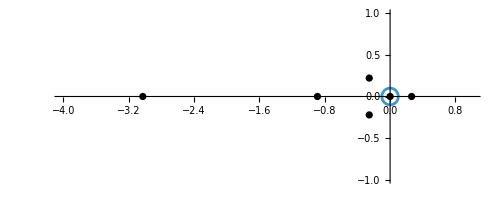

```mathematica
Show[
ParametricPlot[ReIm[upath[t]],{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@Join[U0,{0,-8/9}]]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[l0,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,2}]
```

{{Psi→InterpolatingFunction[…]}}

```mathematica
Mon=Chop[Psi[1]/.First[sol]]
```

{{1.-0.368208 ⅈ,1.20398×10^-9+0.585934 ⅈ},{-1.61028×10^-7-0.231386 ⅈ,1.+0.368208 ⅈ}}

```mathematica
Pi1=Series[1+c[1]U+c[2] U^2+c[3] U^3+c[4] U^4+c[5] U^5+c[6] U^6,{U,0,6}];
Pi2=Pi1 Log[U]+b[1]U+b[2] U^2+b[3] U^3+b[4] U^4+b[5] U^5+b[6] U^6;
```

```mathematica
A5[f_,U_]:=(2 U (-32-282 U-294 U^2-99 U^3) f+(8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) D[f,U]+U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) D[f,{U,2}])/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4));
```

```mathematica
sol1=Solve[Simplify[Series[A5[Pi1,U], {U,0,6}]]==0, Array[c,6]]
```

{{c[1]→0,c[2]→2,c[3]→6,c[4]→6,c[5]→60,c[6]→110}}

```mathematica
sol2=Solve[Simplify[Series[A5[Pi2/.First[sol1],U], {U,0,6}]]==0,Array[b,6]]
```

{{b[1]→1/8,b[2]→31/16,b[3]→139/24,b[4]→279/32,b[5]→7843/120,b[6]→400/3}}

```mathematica
{sPi1,sPi2}={Pi1,Pi2}/.First[sol1]/.First[sol2]
```

{1+2 U^2+6 U^3+6 U^4+60 U^5+110 U^6+O[U]^7,Log[U]+U/8+1/16 (31+32 Log[U]) U^2+1/24 (139+144 Log[U]) U^3+3/32 (93+64 Log[U]) U^4+1/120 (7843+7200 Log[U]) U^5+10/3 (40+33 Log[U]) U^6+O[U]^7}

```mathematica
A5[#,U]&/@{sPi1,sPi2}
```

{O[U]^5,O[U]^5}

```mathematica
Cmat=Normal[{{sPi1,sPi2},{D[sPi1,U],D[sPi2,U]}}]/.{U->upath[0]}
```

{{102731/100000,1/80+(7843-7200 Log[10])/12000000+(139-144 Log[10])/24000+(3 (93-64 Log[10]))/320000+(40-33 Log[10])/300000+(31-32 Log[10])/1600-Log[10]},{3203/5000,81/8+(9283-7200 Log[10])/240000+1/800 (187-144 Log[10])+(91-66 Log[10])/10000+(3 (109-64 Log[10]))/8000+1/80 (47-32 Log[10])}}

```mathematica
Cmat=Normal[{{sPi1/(2 Pi I),-2 sPi2/Pi^2 + m sPi1/(2 Pi I)},{D[sPi1,U]/(2 Pi I),-2 D[sPi2,U]/Pi^2 + m D[sPi1,U]/(2 Pi I)}}]/.{U->upath[0]}/.{m->1/3Log[l0]/(2Pi I)}
```

{{-(102731 ⅈ)/(200000 π),-1/(40 π^2)-(7843-7200 Log[10])/(6000000 π^2)-(139-144 Log[10])/(12000 π^2)-(3 (93-64 Log[10]))/(160000 π^2)-(40-33 Log[10])/(150000 π^2)-(31-32 Log[10])/(800 π^2)+(2 Log[10])/π^2},{-(3203 ⅈ)/(10000 π),-81/(4 π^2)-(9283-7200 Log[10])/(120000 π^2)-(187-144 Log[10])/(400 π^2)-(91-66 Log[10])/(5000 π^2)-(3 (109-64 Log[10]))/(4000 π^2)-(47-32 Log[10])/(40 π^2)}}

```mathematica
Inverse[Cmat].Mon.Cmat//MatrixForm
```

(1.-0.00283997 ⅈ | 8.01212-8.15122×10^-9 ⅈ
1.00799×10^-6-1.37023×10^-8 ⅈ | 1.+0.00283986 ⅈ)

```mathematica
2Pi I//N
```

0.+6.28319 ⅈ

#### the other points

```mathematica
U0
```

{,,,}

```mathematica
upath[t_]:=U0[[2]]+1/10 Exp[2Pi I t];
```

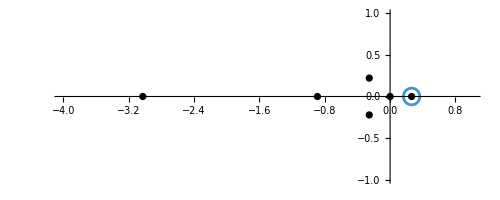

```mathematica
Show[
ParametricPlot[ReIm[upath[t]],{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@Join[U0,{0,-8/9}]]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[l0,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,2}]
```

{{Psi→InterpolatingFunction[…]}}

```mathematica
Mon=Chop[Psi[1]/.First[sol]]
```

{{1.+1.3074 ⅈ,-3.25347×10^-8+0.760449 ⅈ},{1.21613×10^-7-2.24775 ⅈ,1.-1.3074 ⅈ}}

```mathematica
Series[P[l0,U],{U,U0[[2]],1}]//N
```

1/(U-0.263185)+6.49834-18.126 (U-0.263185)+O[U-0.263185]^2

```mathematica
Series[Q[l0,U],{U,U0[[2]],1}]//N
```

2.15458/(U-0.263185)-1.88023-1.0056 (U-0.263185)+O[U-0.263185]^2

```mathematica
A4/.{a->Function[{l,U}, aa[U]]}/.{l->l0}/.{aa->Function[U,(U-U0[[2]])^r]}
Series[%, {U,U0[[2]],2}]//N
```

((-1+r) r U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) (U-)^(-2+r)+r (8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) (U-)^(-1+r)+2 U (-32-282 U-294 U^2-99 U^3) (U-)^r)/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4))

(-0.263185+U)^(-2.+r) ((-1.+r) r+O[U-0.263185]^1)+(-0.263185+U)^r (2.15458/(U-0.263185)-1.88023+O[U-0.263185]^1)+(-0.263185+U)^(-1.+r) (r/(U-0.263185)+6.49834 r+O[U-0.263185]^1)

```mathematica
Pi1=Series[1+c[1](U-U0[[2]])+c[2] (U-U0[[2]])^2+c[3] (U-U0[[2]])^3,{U,U0[[2]],3}];
Pi2=Pi1 Log[U-U0[[2]]]+b[1](U-U0[[2]])+b[2] (U-U0[[2]])^2+b[3] (U-U0[[2]])^3;
Pi3=Series[(U-U0[[2]])+b[2] (U-U0[[2]])^2+b[3] (U-U0[[2]])^3+b[4] (U-U0[[2]])^4,{U,U0[[2]],4}];
```

```mathematica
A4/.{l->l0}/.{a->Function[{l,U},Pi1]}//N//Simplify
```

2.15458/(U-0.263185)+(-1.88023+2.15458 c[1.])+(-1.0056-1.88023 c[1.]+2.15458 c[2.]) (U-0.263185)+(9.92163-1.0056 c[1.]-1.88023 c[2.]+2.15458 c[3.]) (U-0.263185)^2+O[U-0.263185]^3

```mathematica
A5[f_,U_]:=(2 U (-32-282 U-294 U^2-99 U^3) f+(8+16 U-183 U^2-1296 U^3-1412 U^4-396 U^5) D[f,U]+U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4) D[f,{U,2}])/(U (8+9 U) (1+U-8 U^2-36 U^3-11 U^4));
```

```mathematica
sol1=Simplify@Solve[Simplify[Series[A5[Pi1,U], {U,U0[[2]],3}]]==0, Array[c,3]];
```

```mathematica
sol2=Simplify@Solve[Simplify[Series[A5[Pi2/.First[sol1],U], {U,U0[[2]],3}]]==0,Array[b,3]];
```

Series::ztest1: Unable to decide whether numeric quantity -28/11-336/121 Root[-1331-121 #1+88 Slot[«1»]^2+36 Slot[«1»]^3+#1^4&,2,0]-(1481 Root[«1»&,2,0]^2)/1331-(6912 («1»)^3)/14641-8 Root[«1»&,2,0]+119 Root[«1»&,2,0]^2+1008 Root[«5»+11 Power[«2»]&,2,0]^3+1324 Root[-1-Slot[«1»]+8 Power[«2»]+36 Power[«2»]+11 Power[«2»]&,2,0]^4+396 Root[-1-Slot[«1»]+8 Power[«2»]+36 Power[«2»]+11 Power[«2»]&,2,0]^5 is equal to zero. Assuming it is.

```mathematica
{sPi1,sPi2}={Pi1,Pi2}/.First[sol1]/.First[sol2];
```

```mathematica
Cmat=Normal[{{sPi1,sPi2},{D[sPi1,U],D[sPi2,U]}}]/.{U->upath[0]}
```

```mathematica
Inverse[Cmat].Mon.Cmat//MatrixForm
```

(1.-0.00283997 ⅈ | 6.40195×10^-9+6.29271 ⅈ
-1.74463×10^-8-1.28341×10^-6 ⅈ | 1.+0.00283986 ⅈ)

```mathematica
2Pi I//N
```

0.+6.28319 ⅈ

```mathematica
(* 
Pi1 -> 1 + ...;
Pi2 -> Log[U] Pi1 + ...;
om1 -> Log[U] + ...;
om2 -> Log[U]^2/2 + ...;

T   -> Log[U]/(2 Pi I) = om1/(2 Pi I);
TD  -> -Log[U]^2/Pi^2  = -2 om2/Pi^2 -(ⅈ m om1)/(2 π)-m^2/2;

a   -> Pi1/(2 Pi I);
aD  -> -2 Pi2/Pi^2 + m Pi1/(2 Pi I);
*)
```

```mathematica
{ppp1,(Log[U] ppp1+b[1] U+b[2] U^2+b[3] U^3)}/U /.{ppp1->1+a[1] U+a[2] U^2+a[3] U^3}//Expand
Series[Integrate[%,U],{U,0,2}]
```

{1/U+a[1]+U a[2]+U^2 a[3],b[1]+U b[2]+U^2 b[3]+Log[U]/U+a[1] Log[U]+U a[2] Log[U]+U^2 a[3] Log[U]}

{Log[U]+a[1] U+1/2 a[2] U^2+O[U]^3,Log[U]^2/2+(-a[1]+b[1]+a[1] Log[U]) U+1/4 (-a[2]+2 b[2]+2 a[2] Log[U]) U^2+O[U]^3}

```mathematica
Integrate[Log[U]/U,U]
```

Log[U]^2/2

```mathematica
Integrate[Log[U],U]
```

-U+U Log[U]

```mathematica
Integrate[Log[U]U^n,U]
```

(U^(1+n) (-1+(1+n) Log[U]))/(1+n)^2

```mathematica
ZLV[{-1,0,0,0},Log[U]/(2 Pi I),m]
```

-m^2/2-(ⅈ m Log[U])/(2 π)-Log[U]^2/π^2

```mathematica
Solve[Log[U]^2/2==om2,Log[U]]
-Log[U]^2/π^2/.First[%]
```

{{Log[U]→-√2 √om2},{Log[U]→√2 √om2}}

-(2 om2)/π^2

1.4

```mathematica
u0=Truncate;
Series[2Sqrt[2]/(U^2-2),{U,1.414213562373095,1}]
```

-6.36905×10^15-4.05648×10^31 (U-1.41421)+O[U-1.41421]^2

```mathematica
FullForm[u0]
```

1.

## redo

```mathematica
P[l_,U_]:=(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
Q[l_,U_]:=(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
PF[f_,l_,U_]:=D[f,{U,2}] + D[f, {U,1}]P[l,U] + f Q[l, U];
matA[l_,U_]={{0, 1}, {-Q[l,U], -P[l, U]}};
```

```mathematica
l0=1;
```

```mathematica
U0=Join[U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]], {-8/9,0}]
```

{,,,,-8/9,0}

```mathematica
UPath6[t_]:=U0[[6]]+1/10Exp[2Pi I t];
UPath2[t_]:=U0[[2]]+Abs[U0[[2]]-UPath6[0]]Exp[2Pi I (t+1/2)];
UPath4[t_]:=U0[[4]]+2/10Exp[2Pi I t];
UPath3[t_]:=U0[[3]]+2/10Exp[2Pi I t];
```

```mathematica
UPath6To2[t_]:=(1-t)UPath6[0]+t UPath2[1/2]
```

```mathematica
UPathB[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[5]]+I/10}, {3/4,U0[[5]]-I/10}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
UPath1[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[1]]+I/5+1/3}, {3/4,U0[[1]]-I/5+1/3}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

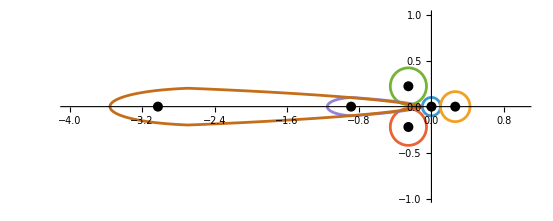

```mathematica
Show[
ParametricPlot[{ReIm[UPath6[t]], ReIm[UPath2[t]], ReIm[UPath4[t]],ReIm[UPath3[t]],ReIm[UPathB[t]],ReIm[UPath1[t]]},{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@U0]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->60];
Mon6=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath2'[t]*matA[l0,UPath2[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon2=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath4'[t]*matA[l0,UPath4[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon4=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath3'[t]*matA[l0,UPath3[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50];
Mon3=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPathB'[t]*matA[l0,UPathB[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50,MaxSteps->100000];
MonB=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath1'[t]*matA[l0,UPath1[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->50,MaxSteps->100000];
Mon1=Psi[1]/.First[sol];
```

```mathematica
Simplify[Series[PF[U^r(1+Sum[a[i](U-U0[[6]])^i,{i,1,2}]),l0,U],{U,U0[[6]],2}]];
```

```mathematica
NumTerms=40;
```

```mathematica
Pi1=(1+Sum[a[i](U-U0[[6]])^i,{i,1,NumTerms}]);
```

```mathematica
Simplify[Series[PF[Pi1,l0,U],{U,U0[[6]],NumTerms}]];
sol=Solve[Thread[%[[3]][[1;;NumTerms]]==0],Array[a,NumTerms]];
Pi1Sol=Pi1/.First[sol];
```

```mathematica
Pi2=Pi1Sol Log[U-U0[[6]]]+Sum[b[i](U-U0[[6]])^i,{i,1,NumTerms}];
```

```mathematica
Simplify[Series[PF[Pi2,l0,U],{U,U0[[6]],NumTerms}]];
sol=Solve[Thread[%[[3]][[1;;NumTerms]]==0],Array[b,NumTerms]];
Pi2Sol=Pi2/.First[sol];
```

```mathematica
(* 
Pi1 -> 1 + ...;
Pi2 -> Log[U] Pi1 + ...;
om1 -> Log[U] + ...;
om2 -> Log[U]^2/2 + ...;

T   -> (Log[U] + 1/3 Log[l])/(2 Pi I) = om1/(2 Pi I) + 1/3Log[l]/(2 Pi I);
TD  -> -Log[U]^2/Pi^2  = -2 om2/Pi^2 -(3 Log[l] om1)/(4 π^2)-Log[l]^2/(8 π^2);

a   -> Pi1/(2 Pi I);
aD  -> -2 Pi2/Pi^2 -(3 Log[l] Pi1)/(4 π^2);
*)
```

```mathematica
PiVec={Pi1Sol/(2 Pi I), -2 Pi2Sol/Pi^2 -(3 Log[l0] Pi1Sol)/(4 π^2)};
```

```mathematica
Cmat6={PiVec,D[PiVec,U]}/.{U->UPath6[0]}
```

{{-(51368826850355454276413201770640727189 ⅈ)/(100000000000000000000000000000000000000 π),-(2 (165135901536864897980359448500996868603722075233951269/4190534476128000000000000000000000000000000000000000000-(51368826850355454276413201770640727189 Log[10])/50000000000000000000000000000000000000))/π^2},{-(1614039884510962922005717358443899597 ⅈ)/(5000000000000000000000000000000000000 π),-(2 (3933004942968408341758083281069305437633977031138793423/356195430470880000000000000000000000000000000000000000-(1614039884510962922005717358443899597 Log[10])/2500000000000000000000000000000000000))/π^2}}

```mathematica
N@LinearSolve[Cmat6, Mon6.Cmat6]//MatrixForm
Round[%]//MatrixForm
```

(1.-1.56935×10^-17 ⅈ | 8.+1.5178×10^-28 ⅈ
-5.53501×10^-30-3.35971×10^-30 ⅈ | 1.+1.56935×10^-17 ⅈ)

(1 | 8
0 | 1)

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6To2'[t]*matA[l0,UPath6To2[t]].Psi[t],
Psi[0]==IdentityMatrix[2]
}, Psi, {t,0,1},WorkingPrecision->60]
Conn=Psi[1]/.First[sol]
```

{{Psi→InterpolatingFunction[…]}}

{{1.0315995224665550921478831853292808350686725957779372180614,0.055528452411420516203466813327248178299884528167490231375882},{1.1034421104727142975020378671803822305396047151053495983008,0.84978863324912869297157623916939705767930041265184080532164}}

```mathematica
N@LinearSolve[Cmat6, Mon6.Cmat6]//MatrixForm
```

(1.-3.94391×10^-9 ⅈ | 8.+1.5178×10^-28 ⅈ
1.94431×10^-18-3.35971×10^-30 ⅈ | 1.+3.94391×10^-9 ⅈ)

```mathematica
N@LinearSolve[Cmat6, Mon2.Cmat6]//MatrixForm
Round[%]
```

(1.-1.79063×10^-9 ⅈ | -3.2064×10^-18-4.4706×10^-23 ⅈ
-1.-2.18604×10^-24 ⅈ | 1.+1.79063×10^-9 ⅈ)

{{1,0},{-1,1}}

```mathematica
{{1,0},{-1,1}}
{Det[%],Tr[%]}
```

{{1,0},{-1,1}}

{1,2}

```mathematica
Cmat4={PiVec,D[PiVec,U]}/.{U->UPath4[0]};
```

```mathematica
N@LinearSolve[Cmat4, Mon4.Cmat4]//MatrixForm
Round[%]
{Det[%],Tr[%],%ᵀ.{{0,1},{-1,0}}.%}
```

(4.02354-0.0562567 ⅈ | 9.07884-0.126807 ⅈ
-1.00691+0.0234066 ⅈ | -2.02354+0.0562567 ⅈ)

{{4,9},{-1,-2}}

{1,2,{{0,1},{-1,0}}}

```mathematica
Cmat3={PiVec,D[PiVec,U]}/.{U->UPath3[0]};
```

```mathematica
N@LinearSolve[Cmat3, Mon3.Cmat3]//MatrixForm
Round[%]
{Det[%],Tr[%],%ᵀ.{{0,1},{-1,0}}.%}
```

(-2.02354-0.0562567 ⅈ | 9.07884+0.126807 ⅈ
-1.00691-0.0234066 ⅈ | 4.02354+0.0562567 ⅈ)

{{-2,9},{-1,4}}

{1,2,{{0,1},{-1,0}}}

```mathematica
CmatB={PiVec,D[PiVec,U]}/.{U->UPath6[1/2]};
```

```mathematica
N@LinearSolve[CmatB, MonB.CmatB]//MatrixForm
Round[%]
```

(1.+9.99978×10^-22 ⅈ | 8.88327×10^-21+3.89701×10^-21 ⅈ
-4.76884×10^-22-1.14142×10^-22 ⅈ | 1.-3.1749×10^-22 ⅈ)

{{1,0},{0,1}}

```mathematica
N@LinearSolve[CmatB, Mon1.CmatB]//MatrixForm
Round[%]
```

(1.+9.50416×10^-19 ⅈ | 1.+7.60135×10^-18 ⅈ
2.33055×10^-22-3.36565×10^-22 ⅈ | 1.-9.50464×10^-19 ⅈ)

{{1,1},{0,1}}

```mathematica
ComplexExpand[Re[Exp[-I psi]Z],Z]
```

Cos[psi] Re[Z]+Im[Z] Sin[psi]

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-dB+dF) m+(dB+2 dF) t-r td

## Monodromies of T and TD

```mathematica
P[l_,U_]:=(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
Q[l_,U_]:=(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
PF[f_,l_,U_]:=D[f,{U,2}] + D[f, {U,1}]P[l,U] + f Q[l, U]
```

```mathematica
Simplify[PF[U D[f[l,U],U],l,U]]
{cf3,cf2,cf1}=Coefficient[%, {Derivative[0,3][f][l,U],Derivative[0,2][f][l,U],Derivative[0,1][f][l,U]}]
```

((8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5) f^(0,1)[l,U]+U ((24+50 U+(27-320 l) U^2-2016 l U^3+4 l (-783+224 l) U^4+54 l (-27+16 l) U^5) f^(0,2)[l,U]+U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4) f^(0,3)[l,U]))/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

{(8 U^2+17 U^3+9 U^4-64 l U^4-360 l U^5-540 l U^6+128 l^2 U^6-243 l U^7+144 l^2 U^7)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),(24 U+50 U^2+27 U^3-320 l U^3-2016 l U^4-3132 l U^5+896 l^2 U^5-1458 l U^6+864 l^2 U^6)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)),(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))}

```mathematica
FullSimplify[cf2/cf3]
```

3/U-9/(8+9 U)+(1+64 l^2 U^3-4 l U (4+27 U (1+U)))/(1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4)

```mathematica
Simplify[cf1/cf3]
```

(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U^2 (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4))

```mathematica
P1[l_,U_]:=3/U-9/(8+9 U)+(1+64 l^2 U^3-4 l U (4+27 U (1+U)))/(1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4);
Q1[l_,U_]:=(8+16 U+(9-256 l) U^2-1860 l U^3+16 l (-189+64 l) U^4+54 l (-27+16 l) U^5)/(U^2 (8+9 U) (1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4));
```

```mathematica
PF1[f_,l_,U_]:=D[f,{U,3}] + D[f, {U,2}]P1[l,U] + D[f,U]* Q1[l, U];
matA1[l_,U_]:={{0,1,0},{0,0,1},{0,-Q1[l,U],-P1[l,U]}};
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA1[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->60];
Non6=Psi[1]/.First[sol];
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPathB'[t]*matA1[l0,UPathB[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->50];
NonB=Psi[1]/.First[sol];
```

```mathematica
PiVec1=Join[{1},Simplify[Integrate[PiVec/U,U]+{1/3Log[l0]/(2 Pi I), -Log[l0]^2/(8 π^2)}]];
```

```mathematica
Dmat6={PiVec1,D[PiVec1,U],D[PiVec1,{U,2}]}/.{U->UPath6[0]};
```

```mathematica
LinearSolve[Dmat6, Non6.Dmat6]
Round[%]ᵀ//MatrixForm
```

{{1.,0.999999999999999994280141173144113598618336350310506372029-7.846755432534487665487549292667218495224×10^-18 ⅈ,4.00000000000000000966436998775683750134564047975805205367-1.532829914134107293003058545310885197595×10^-17 ⅈ},{0,1.00000000000000000000000000139641615828765744744770369037-1.5693510864383899412094015847014583678561×10^-17 ⅈ,8.00000000000000006508761059675406004445207851551120215751-1.10254061879683056146788101547×10^-27 ⅈ},{0,1.18022198320654708241373016512260351275217763504963569969×10^-28+3.48177339929625472901474244762936073801900277793980189835×10^-28 ⅈ,1.00000000000000000000000000105365782639859459994606265987+1.5693510865731844747774189754034596157054×10^-17 ⅈ}}

(1 | 0 | 0
1 | 1 | 0
4 | 8 | 1)

```mathematica
DmatB={PiVec1,D[PiVec1,U],D[PiVec1,{U,2}]}/.{U->UPath6[1/2]};
```

```mathematica
LinearSolve[DmatB, NonB.DmatB]
Round[%]ᵀ//MatrixForm
```

{{1.,-1.34649930149484743994430729124813109969189421038×10^-21+1.81764782524811743217493289134156677374560785538×10^-21 ⅈ,-1.30810740468708496157350244726545025743725612963×10^-20+1.03577470713855339106677593209733636432063498282×10^-20 ⅈ},{0,1.00000000000000000000302395051647209409289066906-8.279347640897160317263878948×10^-21 ⅈ,3.75172697603694818569341675549788427118437092574×10^-20-5.31937703637249456167890883366088951541666430005×10^-20 ⅈ},{0,-1.5074403108776497427770676223359483669375280159×10^-22+2.11489108132383765318779032538137975998570176383×10^-21 ⅈ,0.999999999999999999994830873693605060911952222709+1.479085906993654901309243272×10^-20 ⅈ}}

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## l=-1/10

```mathematica
l0=-1/4;
```

```mathematica
U0=Join[U/.Simplify[Solve[1+U-8 l U^2-36 l U^3+l (-27+16 l) U^4==0/.{l->l0},U]], {-8/9,0}]
```

{,,,,-8/9,0}

```mathematica
UPath6[t_]:=U0[[6]]+1/10Exp[2Pi I t];
UPath2[t_]:=U0[[2]]+Abs[U0[[2]]-UPath6[0]]Exp[2Pi I (t+1/2)];
UPath4[t_]:=U0[[4]]+2/10Exp[2Pi I t];
UPath3[t_]:=U0[[3]]+2/10Exp[2Pi I t];
```

```mathematica
UPath6To2[t_]:=(1-t)UPath6[0]+t UPath2[1/2]
```

```mathematica
UPathB[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[5]]+I/10}, {3/4,U0[[5]]-I/10}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
UPath1[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[1]]+I/5+1/3}, {3/4,U0[[1]]-I/5+1/3}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

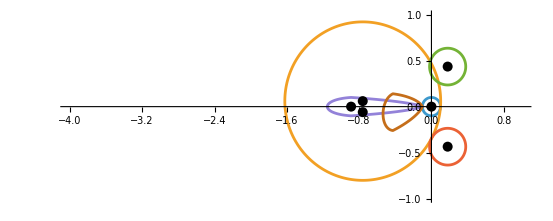

```mathematica
Show[
ParametricPlot[{ReIm[UPath6[t]], ReIm[UPath2[t]], ReIm[UPath4[t]],ReIm[UPath3[t]],ReIm[UPathB[t]],ReIm[UPath1[t]]},{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@U0]}]
]
```

```mathematica
sol=NDSolve[{
Psi'[t]==UPath6'[t]*matA1[l0,UPath6[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->60,MaxSteps->100000];
Non6=Psi[1]/.First[sol];
```

```mathematica
(* now with Richardson sum *)
F1dPeriodsN[λ_,u_,Nn_,Nr_]:=Module[{om1tab,om2tab,om1resum, om2resum,k,l},
om1tab=Table[u^n  Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}],{n,0,Nn}];
om2tab=Table[u^n Sum[k=n-2l; λ^(-k+l)(- If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 l! Gamma[1+k]^2),0]+- If[k<=l&&k+2l>0,( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k!)^2 l! Gamma[1-k+l]),0]),{l,0,Floor[n/2]}],{n,0,Nn}];
om1resum=RichardsonResum[Accumulate[om1tab],Nr];
om2resum=RichardsonResum[Accumulate[om2tab],Nr];
(*{(om2resum-1/4 (8 Log[1/ut]+Log[λ]) om1resum)/om1resum/(2Pi I)}*)
{om1resum,om2resum-1/4 (8 Log[u]+Log[λ]) om1resum}
];
F1PeriodsN[λ_,u_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2resum,varpi3resum,varpi2,varpi3,k,l},
varpi2tab=Table[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[u^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
0 (-2 Log[u]-1/4 Log[λ])(k+2l)!/((l)!(k!)^2(l-k)!)/(k+2l)
+(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2resum=RichardsonResum[Accumulate[varpi2tab],Nr];
varpi3resum=RichardsonResum[Accumulate[varpi3tab],Nr];
(* replace ut by -ut in argument of Log !! *)
varpi2=Log[u]+varpi2resum;
varpi3=Log[u] ^2+(Log[u]+varpi2resum)(-2Log[u]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum;
(*{varpi2,-4(varpi3)/(2Pi I)^2+1/6}*)
{varpi2,varpi3}
 ];
```

```mathematica
Simplify[F1PeriodsN[U l^(1/3),l^(1/3),4,0]]
```

{1/2 l (4+2 U+3 l U^2)+Log[l]/3,1/576 (-(-9+16 U-36 U^2+72 (2+3 l) U^3+1440 l U^4+576 l U^5+1872 l^2 U^6)/U^4-64 Log[l]^2-72 l (4+2 U+3 l U^2) Log[l^(1/3) U]+72 Log[l^(1/3) U]^2-48 Log[l] (4 l (4+2 U+3 l U^2)+Log[l^(1/3) U]))}

```mathematica
Series[2Pi I PiVec[[1]], {U,0,4}]
```

1+2 U^2+6 U^3+6 U^4+O[U]^5

```mathematica
-1-6 u^3-2 u^2 λ-6 u^4 λ^2/.{u->U l^(1/3),λ->l^(1/3)}/.{l->1}
```

-1-2 U^2-6 U^3-6 U^4

```mathematica
A1=Series[F1dPeriodsN[λ,u,5,0],{u,0,5}]
```

{-1-2 λ u^2-6 u^3-6 λ^2 u^4-60 λ u^5+O[u]^6,1/4 (8 Log[u]+Log[λ])+u/(4 λ)+((-1+32 λ^3+32 λ^3 Log[u]+4 λ^3 Log[λ]) u^2)/(8 λ^2)+((1+138 λ^3+144 λ^3 Log[u]+18 λ^3 Log[λ]) u^3)/(12 λ^3)+((-1+24 λ^3+256 λ^6+192 λ^6 Log[u]+24 λ^6 Log[λ]) u^4)/(16 λ^4)+((3-50 λ^3+7890 λ^6+7200 λ^6 Log[u]+900 λ^6 Log[λ]) u^5)/(60 λ^5)+O[u]^6}

```mathematica
Series[-1/2Coefficient[Normal[A1[[2]]],Log[u]], {u,0,5}]
```

-1-2 λ u^2-6 u^3-6 λ^2 u^4-60 λ u^5+O[u]^6

```mathematica
Series[-4Coefficient[Normal[Simplify[A1[[2]]-(-2A1[[1]]Log[u])]], Log[λ]], {u, 0, 5}]
```

-1-2 λ u^2-6 u^3-6 λ^2 u^4-60 λ u^5+O[u]^6

```mathematica
Simplify[A1[[2]]-(-2A1[[1]]Log[u])-(-1/4Log[λ]A1[[1]])]
```

u/(4 λ)+(-1/(8 λ^2)+4 λ) u^2+1/12 (138+1/λ^3) u^3+((-1+24 λ^3+256 λ^6) u^4)/(16 λ^4)+((3-50 λ^3+7890 λ^6) u^5)/(60 λ^5)+O[u]^6

```mathematica
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
u^8 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4)/MirrorCurveDelta[m,u]//Simplify
```

u^8

```mathematica
m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4/.{u->#}
```

m+#1-8 m^2 #1^2-36 m #1^3+(-27+16 m^3) #1^4

```mathematica
uRoot[1,4]
```

```mathematica
P[l_,U_]:=(8+16 U+9 U^2-192 l U^2-1296 l U^3-2052 l U^4+640 l^2 U^4-972 l U^5+576 l^2 U^5)/(U (8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
Q[l_,U_]:=(2 l (-32-282 U-486 U^2+192 l U^2-243 U^3+144 l U^3))/((8+9 U) (1+U-8 l U^2-36 l U^3-27 l U^4+16 l^2 U^4));
PF[f_,l_,U_]:=D[f,{U,2}] + D[f, {U,1}]P[l,U] + f Q[l, U];
```

```mathematica
Simplify[PF[ff[l^(1/3),U l^(1/3)],l,U]/.{l->λ^3, U->u/λ}]/.{(λ^3)^(1/3)->λ, (λ^3)^(2/3) ->λ^2}
{cf2,cf1,cf0}=Coefficient[%, {Derivative[0,2][ff][λ,u],Derivative[0,1][ff][λ,u],ff[λ,u]}]
```

(-2 u λ^2 (282 u λ^2+32 λ^3-9 u^3 (-27+16 λ^3)-6 u^2 λ (-81+32 λ^3)) ff[λ,u]+λ^2 (16 u λ+8 λ^2-1296 u^3 λ^2+u^2 (9-192 λ^3)+36 u^5 (-27+16 λ^3)+4 u^4 λ (-513+160 λ^3)) ff^(0,1)[λ,u]+u λ^2 (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)) ff^(0,2)[λ,u])/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))

{λ^2,(λ^2 (16 u λ+8 λ^2-1296 u^3 λ^2+u^2 (9-192 λ^3)+36 u^5 (-27+16 λ^3)+4 u^4 λ (-513+160 λ^3)))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3))),-(2 λ^2 (282 u λ^2+32 λ^3-9 u^3 (-27+16 λ^3)-6 u^2 λ (-81+32 λ^3)))/((9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))}

```mathematica
Simplify[{cf1,cf0}/cf2]
```

{(16 u λ+8 λ^2-1296 u^3 λ^2+u^2 (9-192 λ^3)+36 u^5 (-27+16 λ^3)+4 u^4 λ (-513+160 λ^3))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3))),-(2 (282 u λ^2+32 λ^3-9 u^3 (-27+16 λ^3)-6 u^2 λ (-81+32 λ^3)))/((9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))}

```mathematica
P2[λ_,u_]:=(16 u λ+8 λ^2-1296 u^3 λ^2+u^2 (9-192 λ^3)+36 u^5 (-27+16 λ^3)+4 u^4 λ (-513+160 λ^3))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)));
Q2[λ_,u_]:=-(2 (282 u λ^2+32 λ^3-9 u^3 (-27+16 λ^3)-6 u^2 λ (-81+32 λ^3)))/((9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)));
PF[f_,λ_,u_]:=D[f,{u,2}] + D[f, {u,1}]P2[λ,u] + f Q2[λ, u];
```

```mathematica
Simplify[PF[u D[f[λ,u],u],λ,u]]
{cf2,cf1,cf0}=Simplify[Coefficient[%, {Derivative[0,3][f][λ,u],Derivative[0,2][f][λ,u],Derivative[0,1][f][λ,u]}]]
Simplify[{cf1,cf0}/cf2]
```

(2 u (-282 u λ^2-32 λ^3+9 u^3 (-27+16 λ^3)+6 u^2 λ (-81+32 λ^3)) f^(0,1)[λ,u])/((9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))+2 f^(0,2)[λ,u]+((16 u λ+8 λ^2-1296 u^3 λ^2+u^2 (9-192 λ^3)+36 u^5 (-27+16 λ^3)+4 u^4 λ (-513+160 λ^3)) (f^(0,1)[λ,u]+u f^(0,2)[λ,u]))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))+u f^(0,3)[λ,u]

{u,(50 u λ+24 λ^2-2016 u^3 λ^2+u^2 (27-320 λ^3)+54 u^5 (-27+16 λ^3)+4 u^4 λ (-783+224 λ^3))/((9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3))),(16 u λ+8 λ^2-1860 u^3 λ^2+u^2 (9-256 λ^3)+54 u^5 (-27+16 λ^3)+16 u^4 λ (-189+64 λ^3))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))}

{(50 u λ+24 λ^2-2016 u^3 λ^2+u^2 (27-320 λ^3)+54 u^5 (-27+16 λ^3)+4 u^4 λ (-783+224 λ^3))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3))),(16 u λ+8 λ^2-1860 u^3 λ^2+u^2 (9-256 λ^3)+54 u^5 (-27+16 λ^3)+16 u^4 λ (-189+64 λ^3))/(u^2 (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)))}

```mathematica
uRoot[λ_,k_]:=Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,k];
```

```mathematica
temp=Simplify[Series[MirrorCurveJ[λ,u],{u,uRoot[λ,1],3}]];
```

```mathematica
Simplify[temp/.{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0}];
```

```mathematica
temp=Simplify[Series[P2[λ,u],{u,uRoot[λ,1],3}]];
```

```mathematica
NumTerms=3;
Pi1=(u-u0)^r(1+Sum[a[i](u-u0)^i,{i,1,NumTerms}]);
```

```mathematica
{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0}
```

```mathematica
temp=Simplify[Series[PF[Series[Pi1,{u,u0,NumTerms}]/.{u0->uRoot[λ,1]}, λ,u], {u,uRoot[λ,1],NumTerms}]];
```

```mathematica
temp/.{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0}
```

(u-u0)^r ((r^2 (540 λ^2-512 λ^5+6912 u0^3 λ^5-48 u0 λ (-27+20 λ^3)+u0^2 (729-1296 λ^3+2048 λ^6)))/(u0 (9 u0+8 λ) (-27+16 λ^3) (1-108 u0^2 λ-16 u0 λ^2+4 u0^3 (-27+16 λ^3)) (u-u0)^2)+1/O[u-u0])

```mathematica
NumTerms=3;
Pi1=(1+Sum[a[i](u-u0)^i,{i,1,NumTerms}]);
```

```mathematica
{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0}
```

```mathematica
temp=Simplify[Series[PF[Series[Pi1,{u,u0,NumTerms}]/.{u0->uRoot[λ,1]}, λ,u], {u,uRoot[λ,1],NumTerms}]];
```

```mathematica
sol=Simplify[Solve[temp==0,Array[a,NumTerms]]]/.{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0}
```

{{a[1]→((-27+16 λ^3) (18 λ+420 u0^2 λ^2+2 u0 (9+32 λ^3)+u0^3 (324 λ-384 λ^4)))/(540 λ^2-512 λ^5+6912 u0^3 λ^5-48 u0 λ (-27+20 λ^3)+u0^2 (729-1296 λ^3+2048 λ^6)),a[2]→(4 (9 u0+8 λ) (λ (6561+972 λ^3-46080 λ^6-11264 λ^9)+3 u0 (2187+56214 λ^3-66048 λ^6+6656 λ^9)+2 u0^2 λ^2 (216513-306180 λ^3+300672 λ^6+31744 λ^9)+3 u0^3 λ (85293-174717 λ^3+448992 λ^6+219904 λ^9)))/(540 λ^2-512 λ^5+6912 u0^3 λ^5-48 u0 λ (-27+20 λ^3)+u0^2 (729-1296 λ^3+2048 λ^6))^2,a[3]→(2 (-27+16 λ^3)^3 (1984 λ^6-2187 u0^12 (-27+16 λ^3)^3+128 u0 λ^5 (83+240 λ^3)-486 u0^11 λ (27-16 λ^3)^2 (-837+352 λ^3)+16 u0^2 λ^4 (1647+51280 λ^3)+4 u0^4 λ^2 (10935+7168092 λ^3-96640 λ^6)-32 u0^3 λ^3 (-1305-225429 λ^3+4096 λ^6)+u0^6 (6561+79777386 λ^3+239147640 λ^6-34639872 λ^9)+4 u0^5 λ (6561+15559128 λ^3+8000544 λ^6-167936 λ^9)+20 u0^7 λ^2 (3046491+37902006 λ^3-13061184 λ^6+131072 λ^9)-18 u0^10 λ^2 (-48138057+61764768 λ^3-24562944 λ^6+2883584 λ^9)+3 u0^8 λ (8640837+443433204 λ^3-270634176 λ^6+30212096 λ^9)-9 u0^9 (-531441-154682136 λ^3+144084096 λ^6-36040704 λ^9+2097152 λ^12)))/(3 (540 λ^2-512 λ^5+6912 u0^3 λ^5-48 u0 λ (-27+20 λ^3)+u0^2 (729-1296 λ^3+2048 λ^6))^3)}}

```mathematica
Pi2=(Pi1/.First[sol])Log[(u-u0)]+(1+Sum[b[i](u-u0)^i,{i,1,NumTerms}]);
```

```mathematica
temp=Simplify[Series[PF[Series[Pi2,{u,u0,NumTerms}]/.{u0->uRoot[λ,1]}, λ,u], {u,uRoot[λ,1],NumTerms}]];
```

```mathematica
sol2=Simplify[Solve[temp==0,Array[b,NumTerms]]]/.{Root[λ+#1-8 λ^2 #1^2-36 λ #1^3+(-27+16 λ^3) #1^4&,1]->u0};
```

## Monodromies again

```mathematica
D[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],u]
```

(u^(-1+n) λ^(-n+3 Floor[n/2]) n! HypergeometricPFQ[{1,n/3-Floor[n/2],1/3+n/3-Floor[n/2],2/3+n/3-Floor[n/2],-Floor[n/2]},{1/2+n/2-Floor[n/2],1/2+n/2-Floor[n/2],1+n/2-Floor[n/2],1+n/2-Floor[n/2]},27/(16 λ^3)])/(((n-2 Floor[n/2])!)^2 Floor[n/2]! (-n+3 Floor[n/2])!)

```mathematica
F1dPeriodsN[λ_,u_,Nn_,Nr_]:=Module[{om1tab,om2tab,om1resum, om2resum,k,l},
om1tab=Table[u^n  Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}],{n,0,Nn}];
om2tab=Table[u^n Sum[k=n-2l; λ^(-k+l)(- If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 l! Gamma[1+k]^2),0]+- If[k<=l&&k+2l>0,( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k!)^2 l! Gamma[1-k+l]),0]),{l,0,Floor[n/2]}],{n,0,Nn}];
om1resum=RichardsonResum[Accumulate[om1tab],Nr];
om2resum=RichardsonResum[Accumulate[om2tab],Nr];
(*{(om2resum-1/4 (8 Log[1/ut]+Log[λ]) om1resum)/om1resum/(2Pi I)}*)
{om1resum,om2resum-1/4 (8 Log[u]+Log[λ]) om1resum}
];
F1PeriodsN[λ_,u_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2resum,varpi3resum,varpi2,varpi3,k,l},
varpi2tab=Table[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[u^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
0 (-2 Log[u]-1/4 Log[λ])(k+2l)!/((l)!(k!)^2(l-k)!)/(k+2l)
+(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2resum=RichardsonResum[Accumulate[varpi2tab],Nr];
varpi3resum=RichardsonResum[Accumulate[varpi3tab],Nr];
(* replace ut by -ut in argument of Log !! *)
varpi2=Log[u]+varpi2resum;
varpi3=Log[u] ^2+(Log[u]+varpi2resum)(-2Log[u]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum;
(*{varpi2,-4(varpi3)/(2Pi I)^2+1/6}*)
{varpi2/(2Pi I),(-4varpi3/(2Pi I)^2+1/6)}
 ];
```

```mathematica
ClearAll[F1Series];
F1LSeries[λ_,u_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2dtab, varpi3dtab, varpi2ddtab, varpi3ddtab,k,l},
varpi2tab=Table[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[u^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2dtab=Table[n u^(n-1) Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3dtab=Table[n u^(n-1) Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2ddtab=Table[n (n-1)u^(n-2) Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,2,Nn}];
varpi3ddtab=Table[n (n-1)u^(n-2)Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,2,Nn}];
{{RichardsonResum[Accumulate[varpi2tab],Nr],RichardsonResum[Accumulate[varpi3tab],Nr]}, {RichardsonResum[Accumulate[varpi2dtab],Nr],RichardsonResum[Accumulate[varpi3dtab],Nr]}, {RichardsonResum[Accumulate[varpi2ddtab],Nr],RichardsonResum[Accumulate[varpi3ddtab],Nr]}}
 ];
```

```mathematica
P3[λ_,u_]:=(50 u λ+24 λ^2-2016 u^3 λ^2+u^2 (27-320 λ^3)+54 u^5 (-27+16 λ^3)+4 u^4 λ (-783+224 λ^3))/(u (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)));
Q3[λ_,u_]:=(16 u λ+8 λ^2-1860 u^3 λ^2+u^2 (9-256 λ^3)+54 u^5 (-27+16 λ^3)+16 u^4 λ (-189+64 λ^3))/(u^2 (9 u+8 λ) (u+λ-36 u^3 λ-8 u^2 λ^2+u^4 (-27+16 λ^3)));
PF1[f_,λ_,u_]:=D[f,{u,3}] + D[f, {u,2}]P3[λ,u] + D[f,u] Q3[λ, u];
matA[λ_,u_]={{0,1,0},{0,0,1},{0,-Q3[λ,u],-P3[λ,u]}};
```

```mathematica
F1PeriodsN[1,N[1/10,200],500,3]
```

{0.3645106298356181670953215474670332951124349404320213881047781448807056198842854634647682820629281044038215289466709951739423426483976705140487237572094784633144878708067777773101097102576377237 ⅈ,-0.3685930912288549417533091144923001988548956024352413310413234230179827971662836902626698013699185803212942357997042164297653663915375030779771021747560578677760612902911053516797030951307185339}

```mathematica
temp=Simplify[{varpi2/(2Pi I),(-4varpi3/(2Pi I)^2+1/6)}/.{varpi2->Log[u]+varpi2resum, varpi3->Log[u] ^2+(Log[u]+varpi2resum)(-2Log[u]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum}/.{varpi2resum->be2[u],varpi3resum->be3[u]}]
temp=Simplify[{%, D[%, u], D[%, {u, 2}]}]
```

{-(ⅈ (be2[u]+Log[u]))/(2 π),1/6+(be3[u]+Log[u]^2+Log[λ]^2/8-1/4 (be2[u]+Log[u]) (8 Log[u]+Log[λ]))/π^2}

{{-(ⅈ (be2[u]+Log[u]))/(2 π),1/6+(be3[u]+Log[u]^2+Log[λ]^2/8-1/4 (be2[u]+Log[u]) (8 Log[u]+Log[λ]))/π^2},{-(ⅈ (1/u+be2'[u]))/(2 π),-(8 be2[u]+8 Log[u]+Log[λ]+u (8 Log[u]+Log[λ]) be2'[u]-4 u be3'[u])/(4 π^2 u)},{-(ⅈ (-1/u^2+be2''[u]))/(2 π),1/(4 π^2 u^2)(-8+8 be2[u]+8 Log[u]+Log[λ]-16 u be2'[u]-8 u^2 Log[u] be2''[u]-u^2 Log[λ] be2''[u]+4 u^2 be3''[u])}}

```mathematica
v=F1LV[1,N[1/10,200],500,3];
```

```mathematica
temp/.Thread[{be2[u],be3[u]}->v]/.{λ->1,u->N[1/10,200]}
```

{0.3645106298356181670953215474670332951124349404320213881047781448807056198842854634647682820629281044038215289466709951739423426483976705140487237572094784633144878708067777773101097102576377237 ⅈ,-0.3685930912288549417533091144923001988548956024352413310413234230179827971662836902626698013699185803212942357997042164297653663915375030779771021747560578677760612902911053516797030951307185339}

```mathematica
ClearAll[SystemMatrix];
SystemMatrix[{{t_,td_},{dt_,dtd_},{ddt_,ddtd_}},λ_,u_] := Transpose@Prepend[Transpose[{{-(ⅈ (t+Log[u]))/(2 π),1/6+(td+Log[u]^2+Log[λ]^2/8-1/4 (t+Log[u]) (8 Log[u]+Log[λ]))/π^2},{-(ⅈ (dt+1/u))/(2 π),-(8 t-4 dtd u+8 (1+dt u) Log[u]+Log[λ]+dt u Log[λ])/(4 π^2 u)},{-(ⅈ (ddt-1/u^2))/(2 π),(-8+8 t-16 dt u+4 ddtd u^2+(8-8 ddt u^2) Log[u]+Log[λ]-ddt u^2 Log[λ])/(4 π^2 u^2)}}],{1,0,0}];
```

```mathematica
ClearAll[ComputeTransition];
ComputeTransition[λ_, upath_,SystMat_]:=Module[{sol,Psi,mon},
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[λ,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->60,MaxSteps->10^6];
mon=Psi[1]/.First[sol];
LinearSolve[SystMat, mon.SystMat]
];
```

```mathematica
ClearAll[ComputeTransition];
Options[ComputeTransition]={WorkingPrecision->60};
ComputeTransition[λ_,upath_, Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi,mon,SystMat, msg, tt=0},
Monitor[
msg="Integrating the connection...";
sol=NDSolve[{
Psi'[t]==upath'[t]*matA[λ,upath[t]].Psi[t],
Psi[0]==IdentityMatrix[3]
}, Psi, {t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^6, StepMonitor:>(tt=t)];
mon=Psi[1]/.First[sol];
msg="Solving for the system matrix...";
SystMat=SystemMatrix[F1LV[λ,upath[0],Nn,Nr],λ,upath[0]];
LinearSolve[SystMat, mon.SystMat], msg<>" "<>ToString[Floor[100tt]]<>"%."]
];
```

```mathematica
uRoot[-11/17,1]
```

```mathematica
λ0=Exp[2Pi I (-1/10)];
up0=With[{k=4},Interpolation[{{0,1/10I}, {1/3,Echo@URoot[λ0,k]+1/10+1/10I },  {2/3,URoot[λ0,k]-1/10},  {1,1/10I}},PeriodicInterpolation->True]]
```

InterpolatingFunction[…]

```mathematica
(*Clear[up0];
up0[t_]:=1/10Exp[2Pi I t];*)
```

```mathematica
λPath[m_]:=Exp[2Pi I m];

rhs[m_,uu_]:=Evaluate@Simplify[-(D[MirrorCurveDelta[λ,u],λ]/. {λ->λPath[m],u->uu})/(D[MirrorCurveDelta[λ,u],u]/. {λ->λPath[m],u->uu})*(λPath'[m])];

u0=u/. Solve[MirrorCurveDelta[λPath[0],u]==0,u];
labels={2,1,4,3};

sol=First@Monitor[NDSolve[Join[Table[Subscript[u,k]'[m]==rhs[m,Subscript[u,k][m]],{k,4}],Table[Subscript[u,k][0]==u0[[k]],{k,4}]],Table[Subscript[u,k],{k,4}],{m,0,4}, WorkingPrecision->60, MaxSteps->10^7,StepMonitor:>(mGlobal=m;)], ProgressIndicator[mGlobal/4]];

us[m_]:=Table[Subscript[u,k][m]/. sol,{k,4}];
```

```mathematica
us[0][[labels[[4]]]]
```

-0.25509866872631505118854853241696430997562377161423416289635-0.22155281435882830055138998551118764205143419882116529272972 ⅈ

```mathematica
Line
```

```mathematica
Manipulate[With[{},
Show[{
Graphics[{Black,PointSize[.012],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Blue, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[m],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[m]/9],{-2,0}],
Directive[Thickness[.001],Dashed,Black],Table[HalfLine[{0,0},ReIm[Exp[2Pi I k/6]]],{k,0,5}]
}
]
},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True,Frame->True]], {{m, 0}, 0, 4,.001}]
```

```mathematica
UPath0[t_]:=1/10Exp[2Pi I t];
```

```mathematica
UPath1=Interpolation[{{0,1/10}, {1/4, #+I/10}, {2/4, #+1/10}, {3/4, #-I/10}, {1, 1/10}}&[us[0][[labels[[1]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath2=Interpolation[{{0,-1/10}, {1/4, #+I/10}, {2/4, #-1/2}, {3/4, #-I/10}, {1, -1/10}}&[us[0][[labels[[2]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPathB=Interpolation[{{0,-1/10}, {1/4, #+I/10}, {2/4, #-1/5}, {3/4, #-I/10}, {1, -1/10}}&[-8/9λPath[0]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath3=Interpolation[{{0,-1/10}, {1/4, #+1/10}, {2/4, #+I/10}, {3/4, #-1/10}, {1, -1/10}}&[us[0][[labels[[3]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath4=Interpolation[{{0,-1/10}, {1/4, #+1/10}, {2/4, #-I/10}, {3/4, #-1/10}, {1, -1/10}}&[us[0][[labels[[4]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

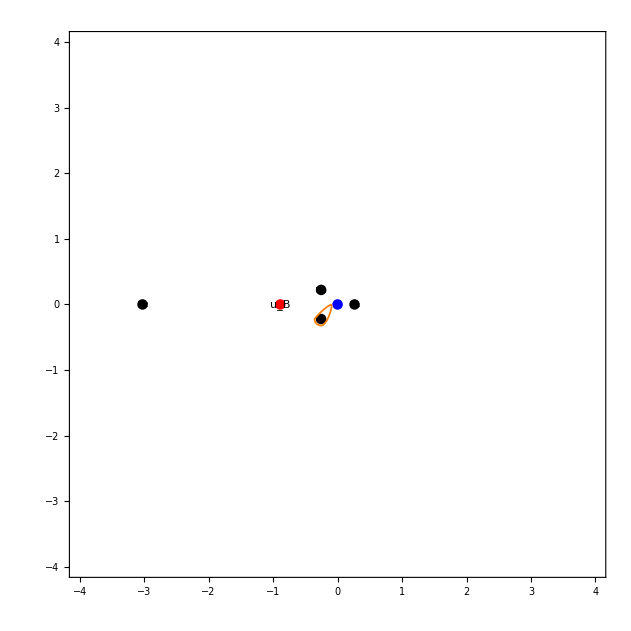

```mathematica
With[{m=0},
Show[{
Graphics[{Black,PointSize[.012],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Blue, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[m],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[m]/9],{-2,0}]}
],
ParametricPlot[ReIm[UPath4[t]],{t,0,1},
PlotStyle->Directive[Thickness[.002], Orange]
]
},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True,Frame->True]
]
```

```mathematica
temp=ComputeTransition[λPath[0], UPath4,256,4, WorkingPrecision->50]
```

{{1.,1.4999999999999999999999376416890916132313632843-2.48756187889628235465365×10^-24 ⅈ,7.4999999999999999999996880060401358918156562269-4.63275780988648788107091×10^-23 ⅈ},{0,-3.9999999999999999999997325568385661897786698423-1.158109488080025017389998×10^-22 ⅈ,-24.99999999999999999999858895401555087017961358-4.793969506133855529384042×10^-22 ⅈ},{0,0.99999999999999999999994702311202574232606479294+4.838728651153135510997067×10^-23 ⅈ,5.9999999999999999999997104711943970178074527942+2.309436525881961469594572×10^-22 ⅈ}}

```mathematica
Mo0=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
1. | 1. | 0.
4. | 8. | 1.)

```mathematica
Mo1=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
0. | 1. | 1.
0. | 0. | 1.)

```mathematica
Mo2=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
0. | 1. | 0.
-0.5 | 1. | 1.)

```mathematica
MoB=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

```mathematica
Mo3=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
-0.5 | 4. | -1.
-1.5 | 9. | -2.)

```mathematica
Mo4=MatrixForm[N[Chop[temp]]ᵀ]
```

(1. | 0. | 0.
1.5 | -4. | 1.
7.5 | -25. | 6.)

```mathematica
Round[temp]
```

{{1,0,-1},{0,4,9},{0,-1,-2}}

```mathematica
a1=Round[temp]
```

{{1,1,4},{0,1,8},{0,0,1}}

```mathematica
a2=Round[temp]
```

{{1,1,4},{0,1,8},{0,0,1}}

```mathematica
a3=Round[temp]
```

{{1,1,4},{0,1,8},{0,0,1}}

```mathematica
UPath6[t_]:=uRoot[-1/4,1][[6]]+1/10Exp[2Pi I t];
UPath2[t_]:=U0[[2]]+Abs[U0[[2]]-UPath6[0]]Exp[2Pi I (t+1/2)];
UPath4[t_]:=U0[[4]]+2/10Exp[2Pi I t];
UPath3[t_]:=U0[[3]]+2/10Exp[2Pi I t];
```

```mathematica
UPath6To2[t_]:=(1-t)UPath6[0]+t UPath2[1/2]
```

```mathematica
UPathB[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[5]]+I/10}, {3/4,U0[[5]]-I/10}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
UPath1[t_]:=Interpolation[N[{{0, UPath6[1/2]},{1/4,U0[[1]]+I/5+1/3}, {3/4,U0[[1]]-I/5+1/3}, {1,UPath6[1/2]}}, 100], PeriodicInterpolation->True][t];
```

```mathematica
Show[
ParametricPlot[{ReIm[UPath6[t]], ReIm[UPath2[t]], ReIm[UPath4[t]],ReIm[UPath3[t]],ReIm[UPathB[t]],ReIm[UPath1[t]]},{t,0,1},
PlotRange->{{-4,1},{-1,1}}
],
Graphics[{Black,PointSize[.013],Point[ReIm/@U0]}]
]
```

-Graphics-

### try again

```mathematica
UPath0[t_]:=1/10Exp[2Pi I (t+1/4)];
```

```mathematica
UPath1=Interpolation[{{0,I/10}, {1/4, #-I/10}, {2/4, #+1/10}, {3/4, #+I/10}, {1, I/10}}&[us[0][[labels[[1]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPathB=Interpolation[{{0,I/10}, {1/4, #+I/10}, {2/4, #-1/5}, {3/4, #-I/10}, {1, I/10}}&[-8/9λPath[0]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath3=Interpolation[{{0,I/10}, {1/4, #+1/10}, {2/4, #+I/10}, {3/4, #-2/10}, {1, I/10}}&[us[0][[labels[[3]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath4=Interpolation[{{0,I/10}, {1/4, #-1/10}, {2/4, #-I/10}, {3/4, #+1/10}, {1, I/10}}&[us[0][[labels[[4]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath2=Interpolation[{{0,I/10}, {1/2-1/8, #-1/10}, {1/2, #-I/10}, {1/2+1/8, #+1/10}, {1, I/10}}&[us[0][[labels[[2]]]]], PeriodicInterpolation->True]
```

```mathematica
<<MaTeX`;
texStyle={FontSize->12, FontFamily->"Times New Roman"}; 
SetOptions[MaTeX,FontSize->12,"Preamble"->{"\\usepackage[english]{babel}","\\usepackage{amsmath,amssymb}", "\\usepackage{lmodern}"}];
imgWidth=218;
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
```

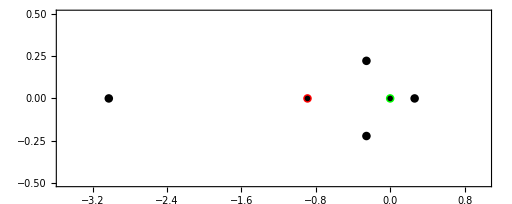

```mathematica
With[{m=0},
Show[{
Graphics[{Black,PointSize[.012],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Green, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[MaTeX["u_"<>ToString[#1]],ReIm[#2],#3]&,
{
labels,
us[m],
{{-1,1},{-3/2,1},{-2,0},{-2,0}} 
}
]~Join~{Text[MaTeX["u_B"],ReIm[-8 λPath[m]/9],{-1,1}], Text[MaTeX["u_0"],ReIm[0],{-1,1}]}
](*,
ParametricPlot[ReIm[UPath2[t]],{t,0,1},
PlotStyle->Directive[Thickness[.002], Orange]
]*)
},PlotRange->{{-3.5,1},{-.5,.5}},AspectRatio->Automatic,Axes->True,Frame->True]
]
```

```mathematica
λPath[0]
```

1

```mathematica
{UPath0[0], UPath1[0], UPath2[0], UPath3[0], UPath4[0], UPathB[0]}
```

{ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10}

```mathematica
temp=ComputeTransition[λPath[0], UPath0,256,4, WorkingPrecision->50];
No0=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{1.,1.,0.},{4.,8.,1.}}

```mathematica
(* Ch[0, 0] *)
temp=ComputeTransition[λPath[0], UPath1,256,4, WorkingPrecision->50];
No1=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,-1.},{0.,0.,1.}}

```mathematica
(* {0, x, -1-2x, -1/2} or {0, -x, 1+2x, 1/2} *)
temp=ComputeTransition[λPath[0], UPath2,256,4, WorkingPrecision->50];
No2=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,0.},{-0.5,1.,1.}}

```mathematica
temp=ComputeTransition[λPath[0], UPathB,256,4, WorkingPrecision->50];
NoB=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
(* Ch[1, 1] *)
temp=ComputeTransition[λPath[0], UPath3,256,4, WorkingPrecision->50];
No3=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-0.5,4.,-1.},{-1.5,9.,-2.}}

```mathematica
(* Ch[2, 1] *)
temp=ComputeTransition[λPath[0], UPath4,256,4, WorkingPrecision->50];
No4=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-1.5,6.,-1.},{-7.5,25.,-4.}}

```mathematica
MatrixForm@MonodromyFromSphericalTwist[Ch[0,0]/.repCh][[{1,3,4},{1,3,4}]]
```

(1 | 0 | 0
0 | 1 | -1
0 | 0 | 1)

```mathematica
MatrixForm[No1]
```

(1. | 0. | 0.
0. | 1. | -1.
0. | 0. | 1.)

```mathematica
MatrixForm@MatrixPower[MonodromyFromSphericalTwist[Ch[2,1]/.repCh][[{1,3,4},{1,3,4}]], 1]
```

(1 | 0 | 0
-3/2 | 6 | -1
-15/2 | 25 | -4)

```mathematica
MatrixForm[No4]
```

(1. | 0. | 0.
-1.5 | 6. | -1.
-7.5 | 25. | -4.)

```mathematica
Solve[{1+2 p+q==6, -p q+q^2/2==-3/2},{p,q}]
```

{{p→2,q→1},{p→7/4,q→3/2}}

```mathematica
MatrixForm[No2]
```

(1. | 0. | 0.
0. | 1. | 0.
-0.5 | 1. | 1.)

```mathematica
MatrixForm@MatrixPower[MonodromyFromSphericalTwist[{0,x,-1-2x,-1/2}][[{1,3,4},{1,3,4}]], 1]
```

(1 | 0 | 0
0 | 1 | 0
-1/2 | 1 | 1)

```mathematica
Solve[{-ch2(-1) ==1/2},{dB,ch2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ch2→1/2}}

```mathematica
MatrixForm@Simplify[MatrixPower[MonodromyFromSphericalTwist[Ch[p+3t,q+2t]/.repCh][[{1,3,4},{1,3,4}]], k]]
```

(1 | 0 | 0
1/2 k (-2 p+q-4 t) (q+2 t) | 1+k (2 p+q+8 t) | -k
1/2 k (q+2 t) (-4 p^2+q^2-24 p t+4 q t-32 t^2) | k (2 p+q+8 t)^2 | 1-k (2 p+q+8 t))

```mathematica
Simplify@MonodromyFromSphericalTwist[SpectralFlow[{r,dF,dB,ch2}, {3k,2k}]]
Simplify[%-MatrixPower[MLV,k].MonodromyFromSphericalTwist[{r,dF,dB,ch2}].MatrixPower[MLV,-k]]
```

{{1,0,0,0},{0,1,0,0},{-r (ch2+k (dB+2 dF+4 k r)),r (-dB+dF+k r),1+dB r+2 dF r+8 k r^2,-r^2},{-((dB+2 dF+8 k r) (ch2+k (dB+2 dF+4 k r))),-((dB-dF-k r) (dB+2 dF+8 k r)),(dB+2 dF+8 k r)^2,1-dB r-2 dF r-8 k r^2}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Mon0=Rationalize[No0]
```

{{1,0,0},{1,1,0},{4,8,1}}

```mathematica
Mon1=Rationalize[No1]
```

{{1,0,0},{0,1,-1},{0,0,1}}

```mathematica
Mon2=Rationalize[No2]
```

{{1,0,0},{0,1,0},{-1/2,1,1}}

```mathematica
Mon3=Rationalize[No3]
```

{{1,0,0},{-1/2,4,-1},{-3/2,9,-2}}

```mathematica
Mon4=Rationalize[No4]
```

{{1,0,0},{-3/2,6,-1},{-15/2,25,-4}}

```mathematica
Dot@@{Mon1,Mon2,Mon3,Mon4}
```

{{1,0,0},{1/2,-4,1},{1/2,3,-1}}

```mathematica
Permute
```

```mathematica
Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Permute[{Mn1,Mn2,Mn3,Mn4}, {4,1,2,3}]
```

{Mn2,Mn3,Mn4,Mn1}

```mathematica
Select[Permutations[{1,2,3,4}], MemberQ[Table[MatrixPower[Mon0,k],{k,-10,10}], Dot@@Permute[{Mon1,Mon2,Mon3,Mon4}, #]]&]
```

{{1,3,2,4}}

```mathematica
Mon1.Mon3.Mon2.Mon4==Inverse[Mon0]
```

True

```mathematica
F1Series[1/10,N[1/30,50],256,4]
```

{{0.0001852737361265211701566559897334993237144,-0.07746621439777946535758237047568786535345},{0.01334668351694804485251652892255481141283,-2.1731138942272456755926451831989377885406},{0.601647839234257413607079043894439879785,7.734769650601918769672517043405681620072}}

### different m

```mathematica
UPath0[t_]:=1/10Exp[2Pi I (t+1/4)];
```

```mathematica
UPath1=Interpolation[{{0,I/10}, {1/4, #-I/10}, {2/4, #+1/10}, {3/4, #+I/10}, {1, I/10}}&[us[1/9][[labels[[1]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPathB=Interpolation[{{0,I/10}, {1/4, #+I/10}, {2/4, #-1/5}, {3/4, #-I/10}, {1, I/10}}&[-8/9λPath[1/9]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath3=Interpolation[{{0,I/10}, {1/2-1/5, #+1/5}, {2/4, #+I/10}, {1/2+1/5, #-1/5}, {1, I/10}}&[us[1/9][[labels[[3]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath4=Interpolation[{{0,I/10}, {1/2-1/5, #-1/5}, {2/4, #-I/5}, {1/2+1/5, #+1/10}, {1, I/10}}&[us[1/9][[labels[[4]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

```mathematica
UPath2=Interpolation[{{0,-I/10}, {1/2-1/8, #-1/10}, {1/2, #-I/10}, {1/2+1/8, #+1/10}, {1, -I/10}}&[us[1/9][[labels[[2]]]]], PeriodicInterpolation->True]
```

InterpolatingFunction[…]

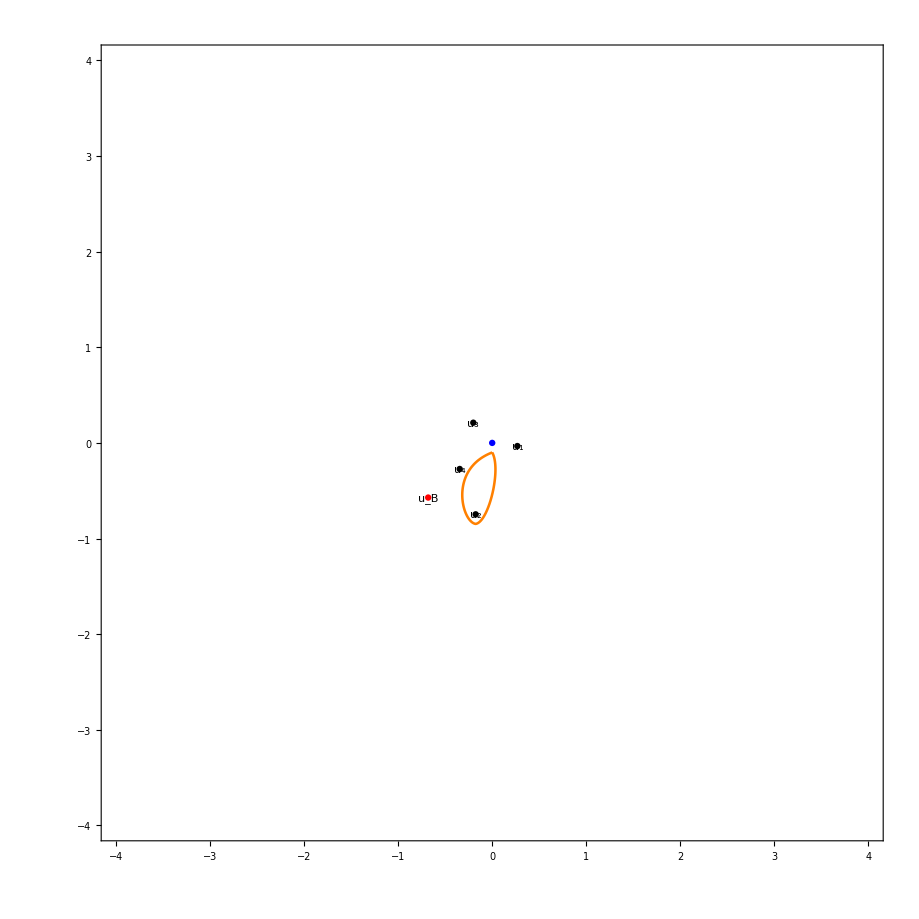

```mathematica
With[{m=1/9},
Show[{
Graphics[{Black,PointSize[.005],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Blue, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[m],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[m]/9],{-2,0}]}
],
ParametricPlot[ReIm[UPath2[t]],{t,0,1},
PlotStyle->Directive[Thickness[.002], Orange]
]
},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True,Frame->True]
]
```

```mathematica
λPath[1/9]
```

ⅇ^((2 ⅈ π)/9)

```mathematica
{UPath0[0], UPath1[0], UPath2[0], UPath3[0], UPath4[0], UPathB[0]}
```

{ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10,ⅈ/10}

```mathematica
temp=ComputeTransition[N[λPath[1/9],100], UPath0,256,4, WorkingPrecision->50];
No0=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{1.,1.,0.},{4.11111,8.,1.}}

```mathematica
(* Ch[0, 0] *)
temp=ComputeTransition[N[λPath[1/9],100], UPath1,256,4, WorkingPrecision->50];
No1=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,-1.},{0.,0.,1.}}

```mathematica
(* {0, x, -1-2x, -1/2} or {0, x, 1-2x, 1/2} *)
temp=ComputeTransition[N[λPath[1/9],100], UPath2,256,4, WorkingPrecision->50];
No2=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-0.111111,-1.,-1.},{0.222222,4.,3.}}

```mathematica
temp=ComputeTransition[λPath[0], UPathB,256,4, WorkingPrecision->50];
NoB=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
(* Ch[1, 1] *)
temp=ComputeTransition[N[λPath[1/9],100], UPath3,256,4, WorkingPrecision->50];
No3=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-0.5,4.,-1.},{-1.5,9.,-2.}}

```mathematica
(* Ch[2, 1] *)
temp=ComputeTransition[N[λPath[1/9],100], UPath4,256,4, WorkingPrecision->50];
No4=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-1.38889,6.,-1.},{-6.94444,25.,-4.}}

```mathematica
Mo4
```

(1. | 0. | 0.
1.5 | -4. | 1.
7.5 | -25. | 6.)

```mathematica
MatrixForm[Inverse[No4]]
```

(1. | 0. | 0.
1.38889 | -4. | 1.
6.94444 | -25. | 6.)

```mathematica
Solve[{1.5+b(1/9)==1.3888888888888893,7.5+d(1/9)==6.944444444444446},{b,d}]
```

{{b→-1.,d→-5.}}

```mathematica
Rationalize[No4]-Mon4
```

{{0,0,0},{1/9,0,0},{5/9,0,0}}

```mathematica
Mon4
```

{{1,0,0},{-3/2,6,-1},{-15/2,25,-4}}

```mathematica
Rationalize[No4]
```

{{1,0,0},{-25/18,6,-1},{-125/18,25,-4}}

```mathematica
Solve[{-15/2+b (1/9)==-125/18},b]
```

{{b→5}}

```mathematica
MatrixForm@MatrixPower[MonodromyFromSphericalTwist[Ch[2,1]/.repCh], 1]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-15/2 | 5 | 25 | -4)

```mathematica
MatrixForm@MonodromyFromSphericalTwist[Ch[0,0]/.repCh][[{1,3,4},{1,3,4}]]
```

(1 | 0 | 0
0 | 1 | -1
0 | 0 | 1)

```mathematica
MatrixForm[No1]
```

(1. | 0. | 0.
0. | 1. | -1.
0. | 0. | 1.)

```mathematica
MatrixForm@MatrixPower[MonodromyFromSphericalTwist[Ch[2,1]/.repCh][[{1,3,4},{1,3,4}]], 1]
```

(1 | 0 | 0
-3/2 | 6 | -1
-15/2 | 25 | -4)

```mathematica
MatrixForm[No4]
```

(1. | 0. | 0.
-1.5 | 6. | -1.
-7.5 | 25. | -4.)

```mathematica
Solve[{1+2 p+q==6, -p q+q^2/2==-3/2},{p,q}]
```

{{p→2,q→1},{p→7/4,q→3/2}}

```mathematica
MatrixForm[No2]
```

(1. | 0. | 0.
0. | 1. | 0.
-0.5 | 1. | 1.)

```mathematica
MatrixForm@MatrixPower[MonodromyFromSphericalTwist[{0,x,-1-2x,-1/2}][[{1,3,4},{1,3,4}]], 1]
```

(1 | 0 | 0
0 | 1 | 0
-1/2 | 1 | 1)

```mathematica
Solve[{-ch2(-1) ==1/2},{dB,ch2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ch2→1/2}}

```mathematica
MatrixForm@Simplify[MatrixPower[MonodromyFromSphericalTwist[Ch[p+3t,q+2t]/.repCh][[{1,3,4},{1,3,4}]], k]]
```

(1 | 0 | 0
1/2 k (-2 p+q-4 t) (q+2 t) | 1+k (2 p+q+8 t) | -k
1/2 k (q+2 t) (-4 p^2+q^2-24 p t+4 q t-32 t^2) | k (2 p+q+8 t)^2 | 1-k (2 p+q+8 t))

```mathematica
Simplify@MonodromyFromSphericalTwist[SpectralFlow[{r,dF,dB,ch2}, {3k,2k}]]
Simplify[%-MatrixPower[MLV,k].MonodromyFromSphericalTwist[{r,dF,dB,ch2}].MatrixPower[MLV,-k]]
```

{{1,0,0,0},{0,1,0,0},{-r (ch2+k (dB+2 dF+4 k r)),r (-dB+dF+k r),1+dB r+2 dF r+8 k r^2,-r^2},{-((dB+2 dF+8 k r) (ch2+k (dB+2 dF+4 k r))),-((dB-dF-k r) (dB+2 dF+8 k r)),(dB+2 dF+8 k r)^2,1-dB r-2 dF r-8 k r^2}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Mon0=Rationalize[No0]
```

{{1,0,0},{1,1,0},{4,8,1}}

```mathematica
Mon1=Rationalize[No1]
```

{{1,0,0},{0,1,-1},{0,0,1}}

```mathematica
Mon2=Rationalize[No2]
```

{{1,0,0},{0,1,0},{-1/2,1,1}}

```mathematica
Mon3=Rationalize[No3]
```

{{1,0,0},{-1/2,4,-1},{-3/2,9,-2}}

```mathematica
Mon4=Rationalize[No4]
```

{{1,0,0},{-3/2,6,-1},{-15/2,25,-4}}

```mathematica
Dot@@{Mon1,Mon2,Mon3,Mon4}
```

{{1,0,0},{1/2,-4,1},{1/2,3,-1}}

```mathematica
Permute
```

```mathematica
Permutations[{1,2,3,4}]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Permute[{Mn1,Mn2,Mn3,Mn4}, {4,1,2,3}]
```

{Mn2,Mn3,Mn4,Mn1}

```mathematica
Select[Permutations[{1,2,3,4}], MemberQ[Table[MatrixPower[Mon0,k],{k,-10,10}], Dot@@Permute[{Mon1,Mon2,Mon3,Mon4}, #]]&]
```

{{1,3,2,4}}

```mathematica
Mon1.Mon3.Mon2.Mon4==Inverse[Mon0]
```

True

```mathematica
F1Series[1/10,N[1/30,50],256,4]
```

{{0.0001852737361265211701566559897334993237144,-0.07746621439777946535758237047568786535345},{0.01334668351694804485251652892255481141283,-2.1731138942272456755926451831989377885406},{0.601647839234257413607079043894439879785,7.734769650601918769672517043405681620072}}

```mathematica
CollInitial
```

{{Ch[0,0],Ch[1,1],Ch[2,1],Ch[2,2]},{Ch[0,0],Ch[0,1],Ch[1,1],Ch[2,2]},{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}}

```mathematica
115200/288
```

400

```mathematica
MatrixForm@MonodromyFromSphericalTwist[Ch[p,q]/.repCh]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-p q+q^2/2 | p-q | 1+2 p+q | -1
(2 p+q) (-p q+q^2/2) | (p-q) (2 p+q) | (2 p+q)^2 | 1-2 p-q)

```mathematica
Mon4
```

{{1,0,0},{-3/2,6,-1},{-15/2,25,-4}}

### Integrating to the cusp (to find the central charge there)

```mathematica
Options[ComputeTransition]={WorkingPrecision->60};
ComputeTransition[λ_,upath_,Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi,mon,SystMat,msg,tt=0},Monitor[msg="Integrating the connection...";
sol=NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA[λ,upath[t]].Psi[t],Psi[0]==IdentityMatrix[3]},Psi,{t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^6,StepMonitor:>(tt=t)];
mon=Psi[1]/. First[sol];
msg="Solving for the system matrix...";
SystMat=SystemMatrix[F1Series[λ,upath[0],Nn,Nr],λ,upath[0]];
LinearSolve[SystMat,mon.SystMat],msg<>" "<>ToString[Floor[100 tt]]<>"%."]];
```

```mathematica
UPathTmp[t_]:=(1-t)(I/10)+t us[0][[labels[[2]]]];
```

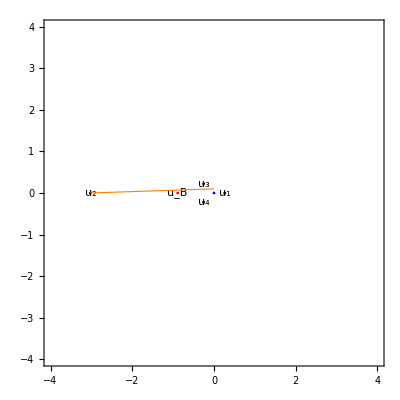

```mathematica
With[{m=0},
Show[{
Graphics[{Black,PointSize[.005],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Blue, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[m],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[m]/9],{-2,0}]}
],
ParametricPlot[ReIm[UPathTmp[t]],{t,0,1},
PlotStyle->Directive[Thickness[.002], Orange]
]
},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True,Frame->True]
]
```

```mathematica
tmp=ComputeTransition[1, UPathTmp, 256, 4]
```

{{1.,0.1360373202798004198307913776791857740698846306062356753905-0.6190242488959148834118729724093728969589647530009519900034 ⅈ,2.223507253190562873442351370740912422848854446328834805784+0.8691110544288341815294952331569133012018110664545398871666 ⅈ},{0,3.613173564864034018315017385968379906616830902450575640307+1.581209622392974115226383962034319035595435047844802679176 ⅈ,-6.011161392578743363499969543316565426330938088332636882071+9.319107002120523699308334571370997879921002811816918812114 ⅈ},{0,-0.711449583525782271968994931060072760594454213037321621797+1.102960703014263165676265138603765195170848563560077227691 ⅈ,-2.930437194960674879594835289173180943501804062394877376657-2.639656213633020658568584863081560449516791760688352827453 ⅈ}}

```mathematica
MatrixForm[N[tmp]]
```

(1. | 0.136037-0.619024 ⅈ | 2.22351+0.869111 ⅈ
0. | 3.61317+1.58121 ⅈ | -6.01116+9.31911 ⅈ
0. | -0.71145+1.10296 ⅈ | -2.93044-2.63966 ⅈ)

```mathematica
MatrixForm@N[SystemMatrix[F1Series[N[1,100], UPathTmp[1],256,4],N[1,100],UPathTmp[1]]]
```

(1. | -0.128715+0.312103 ⅈ | -0.158558-0.316535 ⅈ
0. | 0.744308-0.821535 ⅈ | 1.24647+2.73936 ⅈ
0. | -8.24939-0.39116 ⅈ | 8.27503-29.7265 ⅈ)

```mathematica
PicardFuchsA
```

```mathematica
tmp=SystemMatrix[F1Series[N[1,100], UPathTmp[0],256,4],N[1,100],UPathTmp[0]];
```

```mathematica
sol1=Monitor[NDSolve[{Psi'[t]==UPathTmp'[t]*PicardFuchsA[N[1,100],UPathTmp[t]].Psi[t],Psi[0]==tmp},Psi,{t,0,1},WorkingPrecision->20,MaxSteps->10^6,StepMonitor:>(tt=t)], ProgressIndicator[tt]];
tmp1=Psi[1]/. First[sol1]
```

NDSolve::ndsz: At t == 0.99999999999999995383, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{1.,0.50000000012809+5.7091×10^-12 ⅈ,1.2690301363372+7.0918×10^-10 ⅈ},{0,-3.×10^-10+0.007932347 ⅈ,-0.06+0.0317711 ⅈ},{0,0``-6.180182930666591+0``-6.3876398957971166 ⅈ,0``-14.406232129407053+0``-12.925404915435038 ⅈ}}

```mathematica
Chop[tmp1[[1]]]
```

{1.,0.50000000012809,1.2690301363372+7.0918×10^-10 ⅈ}

```mathematica
{0, x, -1-2x, -1/2}.Sigma.{1,m,0.50000000012808815163037334805551381578`14.884700604338772,1.26903013633715600733641026831577391931`14.828917555698581+7.0917998725014350092088477595`6.778875204800264*^-10 ⅈ}/.{m->0}
```

-1.2809×10^-10

```mathematica
(Ch[-2,0]/.repCh).Sigma.{1,m,0.50000000012808815163037334805551381578`14.884700604338772,1.26903013633715600733641026831577391931`14.828917555698581+7.0917998725014350092088477595`6.778875204800264*^-10 ⅈ}/.{m->0}
ComplexExpand[Re[%]]
```

-3.2690301368495-7.0918×10^-10 ⅈ

-3.2690301368495

```mathematica
Solve[-1.26903013633715600733641026831577391931`14.828917555698581+1.00000000025617630326074669611102763156`14.884700604338772 p+0.50000000012808815163037334805551381578`14.884700604338772 q-p q+q^2/2==0,p]//Simplify
```

{{p→(1.2690301363372-0.50000000012809 q-0.5 q^2)/(1.0000000002562-1. q)}}

```mathematica
Table[(1.26903013633715600733641026831577391931`14.828917555698581-1/2(q+q^2))/(1-q),{q,-10,10}]
```

Power::infy: Infinite expression 1/0 encountered.

{-3.97554271487844,-3.473096986366284,-2.970107762629205,-2.466371232957855,-1.96156712338041,-1.45516164394381,-0.946193972732569,-0.43274246591571,0.089676712112385,0.63451506816858,1.2690301363372,ComplexInfinity,1.7309698636628,2.36548493183142,2.91032328788761,3.43274246591571,3.946193972732569,4.455161643943807,4.961567123380406,5.466371232957855,5.970107762629205}

```mathematica
Solve[(1.26903013633715600733641026831577391931`14.828917555698581-0.50000000012808815163037334805551381578`14.828917555698581 q-0.5`14.828917555698581 q^2)/(1.00000000025617630326074669611102763156`14.828917555698581-1.`14.828917555698581 q)==0,q]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q→-2.1697485658716},{q→1.1697485656154}}

```mathematica
MatrixForm[MonodromyFromSphericalTwist[{0, x, -1-2x, -1/2}/.repCh]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
-1/2 | -1-3 x | 1 | 1)

```mathematica
MatrixForm[MonodromyFromSphericalTwist[Ch[2,1]/.repCh]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-15/2 | 5 | 25 | -4)

```mathematica
{{1.,0.,0.},{-1.3888888888888888,6.,-1.},{-6.944444444444445,25.,-4.}}
```

```mathematica
Mo2
```

(1. | 0. | 0.
0. | 1. | 0.
-0.5 | 1. | 1.)

```mathematica
Inverse[No0].No2
```

{{1.,0.,0.},{-0.111111,-1.,-1.},{0.222222,4.,3.}}

```mathematica
{{1.,0.,0.},{-0.1111111111111111,-1.,-1.},{0.2222222222222222,4.,3.}}
```

### period at u_2 for m = 1/9

```mathematica
m0=51/100;
```

```mathematica
UPathTmp[t_]:=(1-t)(-I/10)+t us[m0][[labels[[2]]]];
```

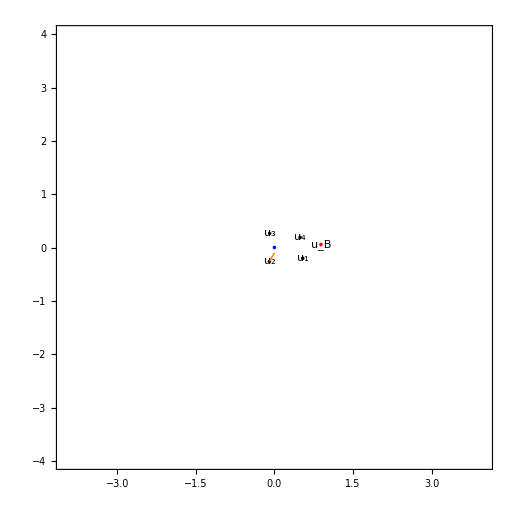

```mathematica
With[{m=m0},
Show[{
Graphics[{Black,PointSize[.005],Point[ReIm/@us[m]],Red,Point[ReIm[-8 λPath[m]/9]], Blue, Point[ReIm[0]]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[m],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[m]/9],{-2,0}]}
],
ParametricPlot[ReIm[UPathTmp[t]],{t,0,1},
PlotStyle->Directive[Thickness[.002], Orange]
]
},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True,Frame->True]
]
```

```mathematica
tmp=SystemMatrix[F1Series[N[λPath[m0],100], UPathTmp[0],256,4],N[λPath[m0],100],UPathTmp[0]];
```

```mathematica
sol1=Monitor[NDSolve[{Psi'[t]==UPathTmp'[t]*PicardFuchsA[N[λPath[m0],100],UPathTmp[t]].Psi[t],Psi[0]==tmp},Psi,{t,0,1},WorkingPrecision->20,MaxSteps->10^6,StepMonitor:>(tt=t)], ProgressIndicator[tt]];
tmp1=Psi[1]/. First[sol1]
```

{{1.,-0.3121809255761335343+0.1783140276475940446 ⅈ,0.4365427767430121466-0.5349420828634916741 ⅈ},{0,5.8492+1.70389 ⅈ,-17.8312-4.12434 ⅈ},{0,-5.8165×10^14+7.372×10^14 ⅈ,1.7449×10^15-2.212×10^15 ⅈ}}

```mathematica
Ch[0,0].Sigma.{1,1/100,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

-0.4365427767430121466+0.5349420828634916741 ⅈ

```mathematica
Ch[-1,0].Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

-0.3221809255907450779+0.178314027568303585 ⅈ

```mathematica
Ch[2,2].Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

-4.309628330199813352+1.604826248749055942 ⅈ

```mathematica
Ch[-4,-2].Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

-4.334733520981676803-1.24819819361244877 ⅈ

```mathematica
Ch[-1,-1].Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

-1.4611544×10^-11-7.92904597×10^-11 ⅈ

```mathematica
(* {0, x, -1-2x, -1/2} or {0, -x, 1+2x, 1/2} *)
```

```mathematica
{0, x, -1-2x, -1/2}.Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh
```

(0.81218092557613353432-0.1783140276475940446 ⅈ)+51/100 (1+3 x)

```mathematica
ComplexExpand@ReIm[Ch[p,q].Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}/.repCh]
Solve[Thread[%==0],{p,q}]
```

{-0.4365427767430121466-0.114361851152267069 p-0.82218092557613353432 q-p q+q^2/2,0.5349420828634916741+0.3566280552951880892 p+0.1783140276475940446 q}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→-0.999999999849719877,q→-0.999999999855892708},{p→-1.63249999981677947,q→0.265000000078226477}}

```mathematica
{0,50,1,-49}.Sigma.{1,m0,tmp1[[1,2]],tmp1[[1,3]]}
ComplexExpand[ReIm[%]]
```

128.02474835554202385+6.813514645443914413 ⅈ

{128.02474835554202385,6.813514645443914413}

```mathematica
MatrixPower[MonodromyFromSphericalTwist[{r,dF,dB,ch2}],k][[{3,4},{3,4}]].{1,t}
Solve[%[[2]]/%[[1]]==t,t]
```

{1+dB k r+2 dF k r-k r^2 t,(dB+2 dF)^2 k+(1-dB k r-2 dF k r) t}

{{t→(dB+2 dF)/r},{t→(dB+2 dF)/r}}

```mathematica
KleinInvariantJ[1/3+.01I]//N
```

-6.03811×10^26+1.04583×10^27 ⅈ

```mathematica
No2
```

{{1.,0.,0.},{-0.111111,-1.,-1.},{0.222222,4.,3.}}

```mathematica
Mon4.Inverse[Mon2].Inverse[Mon4]
```

{{1,0,0},{1,-3,1},{4,-16,5}}

```mathematica
Im[URoot[Exp[2Pi I m],1]*URoot[Exp[2Pi I m],2]]
```

Im[Root[ⅇ^(2 ⅈ m π)+#1-8 ⅇ^(4 ⅈ m π) #1^2-36 ⅇ^(2 ⅈ m π) #1^3+(-27+16 ⅇ^(6 ⅈ m π)) #1^4&,1] Root[ⅇ^(2 ⅈ m π)+#1-8 ⅇ^(4 ⅈ m π) #1^2-36 ⅇ^(2 ⅈ m π) #1^3+(-27+16 ⅇ^(6 ⅈ m π)) #1^4&,2]]

```mathematica
us[1/100][[labels[[{2,4}]]]]
```

{-2.6772822567100356678746430681731202461616458336518137656583-0.97035888372044549645118271068340235772803235051083179224261 ⅈ,-0.26123593452066295775970612160929580095401405276062891386466-0.22375795787203176340426276626151015347620838163388860410853 ⅈ}

```mathematica
us[1/10][[labels[[{2,4}]]]]
```

{-0.21368235373130649354130432303216056381797517489138953101564-0.81197451399571561734351270864045572018948267218269318367223 ⅈ,-0.33356853310447109756467924941741182665311840754021358028556-0.26381174356973899697501103696881231705868997315136931027695 ⅈ}

```mathematica
URoot[Exp[2Pi I 1/10],1]
```

```mathematica
URoot[Exp[2Pi I 1/10],2]
```

```mathematica
URoot[Exp[2Pi I 0],1]
```

```mathematica
URoot[Exp[2Pi I 1/100],2]
```

```mathematica
mC=m/.FindRoot[Im[us[m][[labels[[2]]]]*us[m][[labels[[4]]]]*], {m,1/100}]
```

0.0231639

-(27+256 λ^3)^3

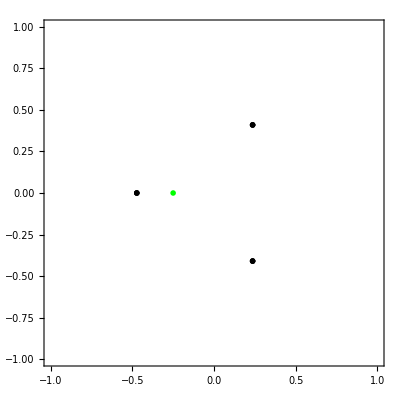

```mathematica
Simplify[Discriminant[MirrorCurveDelta[λ,u], u]]
Graphics[{Black, PointSize[.01], Point[ReIm/@(λ/.Solve[%==0, λ])], Green,Point[ReIm[-1/4]]},
Frame->True, Axes->True, PlotRange->{{-1,1},{-1,1}}
]
```